```mathematica
Series[Sum[j^-(3/2)-ω 4^-j,{j,1,l}],{l,∞,10}]
```

1/3 4^-l (ω+4^l ((-ω+3 Zeta[3/2])-6 √(1/l)+3/2 (1/l)^(3/2)-3/8 (1/l)^(5/2)+7/128 (1/l)^(9/2)-(33 (1/l)^(13/2))/1024+(1287 (1/l)^(17/2))/32768+O[1/l]^(21/2)))

```mathematica
Series[Sum[j^-(3/2),{j,1,l}],{l,∞,10}]
```

Zeta[3/2]-2 √(1/l)+1/2 (1/l)^(3/2)-1/8 (1/l)^(5/2)+7/384 (1/l)^(9/2)-(11 (1/l)^(13/2))/1024+(429 (1/l)^(17/2))/32768+O[1/l]^(21/2)

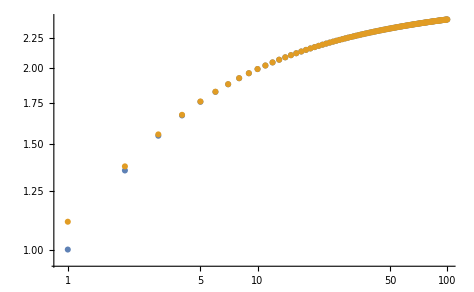

```mathematica
ListLogLogPlot[
{Table[Sum[j^-(3/2),{j,1,l}],{l,1,100}],
Table[Zeta[3/2]-2 √(1/l)+1/2 (1/l)^(3/2),{l,1,100}]}]
```

```mathematica
Sum[4^-j,{j,1,l}]//Simplify
```

1/3-4^-l/3

```mathematica
Table[Sum[j^-(3/2),{j,1,l}],{l,1,100}]-Table[Zeta[3/2]-2 √(1/l)+1/2 (1/l)^(3/2),{l,1,100}]//N
```

{-0.112375,-0.0213851,-0.00789637,-0.00387187,-0.00222332,-0.00141188,-0.000961359,-0.000688975,-0.000513484,-0.000394712,-0.000311105,-0.000250333,-0.000204964,-0.000170321,-0.000143351,-0.000122001,-0.00010485,-0.0000908937,-0.0000794055,-0.0000698517,-0.0000618327,-0.0000550456,-0.0000492573,-0.0000442866,-0.0000399907,-0.0000362563,-0.0000329924,-0.0000301255,-0.0000275956,-0.0000253534,-0.0000233582,-0.0000215761,-0.0000199787,-0.0000185421,-0.000017246,-0.0000160733,-0.0000150093,-0.0000140413,-0.0000131585,-0.0000123515,-0.0000116122,-0.0000109333,-0.0000103087,-9.73298×10^-6,-9.20126×10^-6,-8.70935×10^-6,-8.25347×10^-6,-7.83032×10^-6,-7.43693×10^-6,-7.07066×10^-6,-6.72915×10^-6,-6.4103×10^-6,-6.1122×10^-6,-5.83316×10^-6,-5.57163×10^-6,-5.32623×10^-6,-5.09569×10^-6,-4.87889×10^-6,-4.67479×10^-6,-4.48244×10^-6,-4.30099×10^-6,-4.12966×10^-6,-3.96774×10^-6,-3.81456×10^-6,-3.66954×10^-6,-3.53212×10^-6,-3.4018×10^-6,-3.27811×10^-6,-3.16063×10^-6,-3.04896×10^-6,-2.94274×10^-6,-2.84162×10^-6,-2.74531×10^-6,-2.6535×10^-6,-2.56593×10^-6,-2.48236×10^-6,-2.40255×10^-6,-2.32629×10^-6,-2.25337×10^-6,-2.18361×10^-6,-2.11684×10^-6,-2.05289×10^-6,-1.99162×10^-6,-1.93287×10^-6,-1.87652×10^-6,-1.82245×10^-6,-1.77053×10^-6,-1.72066×10^-6,-1.67273×10^-6,-1.62666×10^-6,-1.58234×10^-6,-1.53969×10^-6,-1.49863×10^-6,-1.45909×10^-6,-1.421×10^-6,-1.38428×10^-6,-1.34888×10^-6,-1.31474×10^-6,-1.28179×10^-6,-1.24998×10^-6}